```mathematica
β = 2;
γ = 1;

{SSsol, IIsol, RRsol} = NDSolveValue[{
SS'[t] == -β*II[t]*SS[t],
II'[t] == β*II[t]*SS[t] - γ*II[t],
RR'[t] == γ*II[t],
SS[0]==0.99, II[0]==0.01, RR[0] == 0
},{SS,II,RR},{t,0,20}];
```

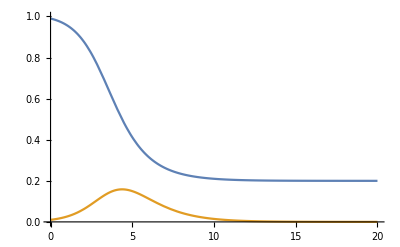

```mathematica
Plot[{SSsol[t],IIsol[t]},{t,0,20}, PlotRange->{0,1}]
```

```mathematica
agam[τ_,Rindiv_:2,μ_:3,σ_:1,ω_:0]:=Piecewise[{
{0,τ<=ω},
{Rindiv*PDF[GammaDistribution[μ^2/σ^2,σ^2/μ],τ-ω],τ>ω}
}];
```

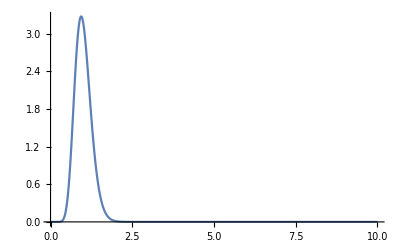

```mathematica
Plot[agam[τ,β/γ,1,0.25,0],{τ,0,10}, PlotRange->All]
```

```mathematica
Integrate[agam[τ],{τ,0,Infinity}]
```

2

```mathematica
NIndiv=1000;
tinfvec = ConstantArray[-1,NIndiv];
tinfvec⟦RandomInteger[{1,NIndiv}]⟧ = 0;
t = 0;
While[t≤10,
(*Assign a look-ahead value*)
del=1;

(*Assign vector for times since infection*)
tinfvecshort = tinfvec⟦Flatten[Position[tinfvec, _?(#≥0&)]]⟧;

(*Count susceptibles*)
ss = Length[tinfvec⟦Flatten[Position[tinfvec, _?(#<0&)]]⟧];

(*Calculate the instantaneous force of infection*)
ffun[t_]:=Total[N[agam[t-#, 2, 1,0.25,0]&/@tinfvecshort]];

(*Integrate the force of infection*)
ftot=NIntegrate[ffun[u],{u,t,t+del}];

(*Calculate the infection rate*)
rate=ss/NIndiv*ftot;

(*Calculate number of new infections*)
ninf=RandomVariate[PoissonDistribution[rate]];

(*If no new infections, continue to next iteration*)
If[ninf==0, t=t+del; Continue[]];

(*If we make it here, there was at least one infection. When?*)
fcdf[δ_]:=(NIntegrate[ffun[u],{u,t,t+δ}]/NIntegrate[ffun[u],{u,t,t+del}]);
draw = Min[RandomVariate[UniformDistribution[],ninf]];
del=FindRoot[fcdf[x]-draw,{x,0.5}]⟦1,2⟧;
Clear[fcdf];

(*Randomly assign the infection to a susceptible*)
newi = RandomChoice[Flatten[Position[tinfvec,_?(#<0&)]]];
tinfvec⟦newi⟧ = t+del;
 (*Update the time*)
t=t+del;

Print[{rate,t,del}];
]
```

NIntegrate::nlim: u = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{1.06544,0.870121,0.870121}

{2.41174,1.77879,0.908673}

{2.29574,1.86157,0.0827772}

{3.33155,2.14264,0.281067}

{4.88956,2.31224,0.169599}

{6.47525,2.60263,0.29039}

{7.86062,2.76621,0.163577}

{8.50769,2.79665,0.0304485}

{9.50084,2.81143,0.0147736}

{10.5581,3.00071,0.18928}

{11.7226,3.16347,0.162767}

{12.5235,3.21313,0.0496557}

{13.511,3.27975,0.0666227}

{14.5764,3.30174,0.0219903}

{15.6574,3.30752,0.00577985}

{16.7178,3.41547,0.107943}

{18.2709,3.47082,0.0553585}

{19.4726,3.47419,0.00336354}

{20.5135,3.4882,0.0140134}

{21.6331,3.53455,0.0463488}

{23.0083,3.53464,0.000088636}

$Aborted

```mathematica
inftimes = Sort[tinfvec⟦Flatten[Position[tinfvec,_?(#≥0&)]]⟧]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,1.18339,3.18339-RandomVariate[UniformDistribution[{0,1}],RandomVariate[PoissonDistribution[0.]]],3.18339-RandomVariate[UniformDistribution[{0,1}],RandomVariate[PoissonDistribution[0.]]],3.18339-RandomVariate[UniformDistribution[{0,1}],RandomVariate[PoissonDistribution[0.]]],3.18339-RandomVariate[UniformDistribution[{0,1}],RandomVariate[PoissonDistribution[0.]]]}

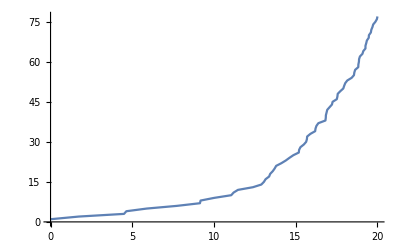

```mathematica
ListLinePlot[{inftimes, Range[1,Length[inftimes]]}ᵀ]
```

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ninf
```

0

```mathematica
RandomChoice[Flatten[Position[tinfvec,_?(#<0&)]]]
```

428

```mathematica
del
```

0.293472

```mathematica
ninf
```

1

```mathematica
draw
```

0.0953881

```mathematica
fcdf[del]
```

fcdf[0.293472]

```mathematica
Min[RandomVariate[UniformDistribution[],10]]
```

0.0239525

```mathematica
ninf
```

1

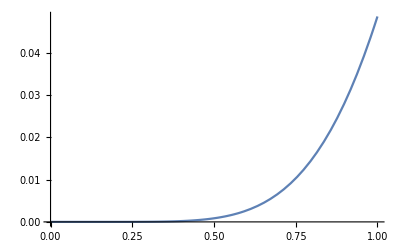

```mathematica
Plot[ffun[τ],{τ,0,1}]
```

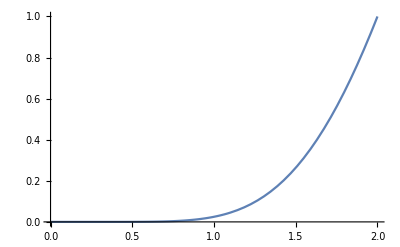

```mathematica
Plot[
NIntegrate[ffun[τ],{τ,0,t}]/NIntegrate[ffun[τ],{τ,0,2}],{t,0,2}, PlotRange->All]
```

```mathematica
Assuming[x>0,NSolve[
(NIntegrate[ffun[τ],{τ,0,x}]/NIntegrate[ffun[τ],{τ,0,2}])==0.5, x]]
```

NIntegrate::nlim: τ = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

```mathematica
?NSolve
```

```mathematica
fcdf[t_]:=(NIntegrate[ffun[τ],{τ,0,t}]/NIntegrate[ffun[τ],{τ,0,1}])
```

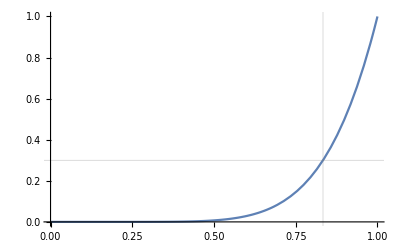

```mathematica
Plot[fcdf[t],{t,0,1}, PlotRange->{0,1}, GridLines->{{0.8334},{0.3}}]
```

```mathematica
FindRoot[fcdf[x]-0.3,{x,0.5}]⟦1,2⟧
```

NIntegrate::nlim: τ = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.833403